Hatano-Nelson Model: Monte Carlo Simulation |

The Hatano-Nelson model is a non-Hermitian Hamiltonian model of fermionic modes exhibiting the so-called skin effect. It was introduced by  Hatano and Nelson in 1996https://doi.org/10.1103/PhysRevLett.77.570, originally, in the context of localization transitions, and later applied to describe vortex pinning in superconductors (Hatano and Nelson, 1997)https://doi.org/10.1103/PhysRevB.56.8651. The non-hermicity and associated skin effect come from quantum dissipative processes through a coupling to the bath (Kawabata, Numasawa and Ryu, 2023)https://doi.org/10.1103/PhysRevX.13.021007.

This tutorial presents a simulation of the quantum master equation of the Hatano-Nelson model.

WickStatepaclet:Q3/ref/WickStateQ3 Package Symbol | Represents a many-fermion quantum state for a non-interacting number-preserving fermions.
WickGaussianpaclet:Q3/ref/WickGaussianQ3 Package Symbol | Non-unitary gate associated with local quadratic non-Hermitian Hamiltonian
WickOperatorpaclet:Q3/ref/WickOperatorQ3 Package Symbol | Represents a non-unitary gate on Wick states
NoisyWickSimulatepaclet:Q3/ref/NoisyWickSimulateQ3 Package Symbol | Simulates the quantum master equation for a dissipative fermionic system

Q3 functions for the Monte Carlo simulation of open quantum systems of non-interacting fermions.

Make sure that Q3 is loaded.

```mathematica
<<Q3`
```

To reproduce exactly the same simulation results, seed the random processor.

```mathematica
SeedRandom[354];
```

Consider a set of fermion modes.

```mathematica
Let[Fermion,c]
```

```mathematica
$L=5;
cc=c[Range@$L]
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5)}

We consider auxiliary fermion modes for convenience. They will be used mainly to describe the quantum jump operators.

```mathematica
aa=a[Range[$L-1]]
bb=b[Range[$L-1]]
```

a[{1,2,3,4}]

b[{1,2,3,4}]

The hopping amplitude.

```mathematica
Let[Real,J]
```

The single-particle Hamiltonian.

```mathematica
hamOp=-J*Hop[cc]//PlusDagger
ham=CoefficientTensor[hamOp,Dagger@cc,cc];
ham//MatrixForm
```

-J (c_(,,1)^(,,†)c_(,,2)+c_(,,2)^(,,†)c_(,,3)+c_(,,3)^(,,†)c_(,,4)+c_(,,4)^(,,†)c_(,,5))-J (c_(,,2)^(,,†)c_(,,1)+c_(,,3)^(,,†)c_(,,2)+c_(,,4)^(,,†)c_(,,3)+c_(,,5)^(,,†)c_(,,4))

(0 | -J | 0 | 0 | 0
-J | 0 | -J | 0 | 0
0 | -J | 0 | -J | 0
0 | 0 | -J | 0 | -J
0 | 0 | 0 | -J | 0)

Construct the quantum jump operators.

```mathematica
a[k_]:=c[k]+I*c[k+1]
b[k_]:=c[k]-I*c[k+1]
ab=Join[aa,Dagger@bb]
```

{c_(,,1)+ⅈ c_(,,2),c_(,,2)+ⅈ c_(,,3),c_(,,3)+ⅈ c_(,,4),c_(,,4)+ⅈ c_(,,5),c_(,,1)^(,,†)+ⅈ c_(,,2)^(,,†),c_(,,2)^(,,†)+ⅈ c_(,,3)^(,,†),c_(,,3)^(,,†)+ⅈ c_(,,4)^(,,†),c_(,,4)^(,,†)+ⅈ c_(,,5)^(,,†)}

```mathematica
jmp=WickOperatorFrom[cc]/@ab
```

{WickOperator[…],WickOperator[…],WickOperator[…],WickOperator[…],WickOperator[…],WickOperator[…],WickOperator[…],WickOperator[…]}

Pick an initial state.

```mathematica
in=Ket[cc->PadRight[{1,0},$L,{1,0}]];
in=WickState[in];
Elaborate[in]
```

1_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))0_(,,c_(,,4))1_(,,c_(,,5))

Set the value of the hopping amplitude J.

```mathematica
ham=ReplaceAllThrough[ham, J->2.0];
ham//MatrixForm
```

(0 | -2. | 0 | 0 | 0
-2. | 0 | -2. | 0 | 0
0 | -2. | 0 | -2. | 0
0 | 0 | -2. | 0 | -2.
0 | 0 | 0 | -2. | 0)

Perform the Monte-Carlo simulation on the Hatano-Nelson model.

WARNING: DO NOT PUT T (the number time steps) TOO LARGE FROM THE BEGINNING. The computation takes long with large T if not exponentially. Increase it gradually after investigating properties for smaller T values.

```mathematica
EchoTiming[data=NoisyWickSimulate[ham,jmp,in,{nT=20,dt=0.1},"Samples"->300];]
Dimensions[data]
```

21.7918

{300,21}

Calculate the entanglement entropy.

```mathematica
EchoTiming[ee=Map[WickEntanglementEntropy[c@{1,2}],data,{2}];]
Dimensions[ee]
```

13.3322

{300,21}

Check the entanglement entropy data.

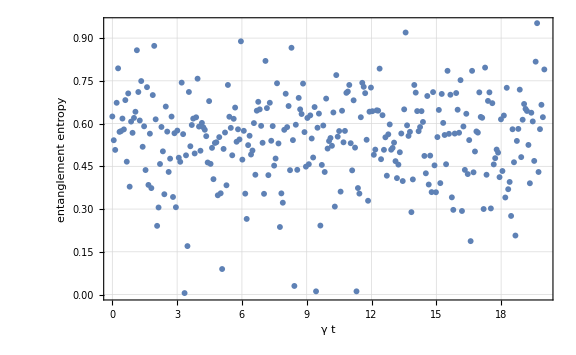

```mathematica
data=Mean/@ee;
ListPlot[data,
DataRange->{0,nT},
FrameLabel->{"γ t","entanglement entropy"}
]
```

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪K. Kawabata, T. Numasawa and S. Ryu (2023)https://doi.org/10.1103/PhysRevX.13.021007, Physical Review X 13, 021007, "Entanglement Phase Transition Induced by the Non-Hermitian Skin Effect."
▪N. Hatano and D. R. Nelson (1996)https://doi.org/10.1103/PhysRevLett.77.570, Physical Review Letters 77, 570, "Localization Transitions in Non-Hermitian Quantum Mechanics."
▪N. Hatano and D. R. Nelson (1997)https://doi.org/10.1103/PhysRevB.56.8651, Physical Review B 56, 287, "Vortex Pinning and Non-Hermitian Quantum Mechanics."
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).